## Results from Python calculations

### Inertial Params

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
(*Data batch generated at:2020-08-03 11:50:20.035126*)adata={{-180.0,-0.001},{-179.0,-0.001},{-178.0,-0.0},{-177.0,-0.0},{-176.0,-0.0},{-175.0,-0.0},{-174.0,-0.0},{-173.0,-0.0},{-172.0,-0.0},{-171.0,-0.0},{-170.0,-0.0},{-169.0,-0.0},{-168.0,0.0},{-167.0,0.0},{-166.0,0.0},{-165.0,0.0},{-164.0,0.0},{-163.0,0.0},{-162.0,0.0},{-161.0,0.0},{-160.0,0.0},{-159.0,0.0},{-158.0,0.001},{-157.0,0.001},{-156.0,0.001},{-155.0,0.001},{-154.0,0.001},{-153.0,0.001},{-152.0,0.001},{-151.0,0.001},{-150.0,0.001},{-149.0,0.001},{-148.0,0.001},{-147.0,0.001},{-146.0,0.001},{-145.0,0.001},{-144.0,0.001},{-143.0,0.001},{-142.0,0.001},{-141.0,0.001},{-140.0,0.001},{-139.0,0.001},{-138.0,0.001},{-137.0,0.001},{-136.0,0.001},{-135.0,0.001},{-134.0,0.002},{-133.0,0.002},{-132.0,0.002},{-131.0,0.002},{-130.0,0.002},{-129.0,0.002},{-128.0,0.002},{-127.0,0.002},{-126.0,0.002},{-125.0,0.002},{-124.0,0.002},{-123.0,0.002},{-122.0,0.002},{-121.0,0.002},{-120.0,0.002},{-119.0,0.002},{-118.0,0.002},{-117.0,0.002},{-116.0,0.002},{-115.0,0.002},{-114.0,0.002},{-113.0,0.002},{-112.0,0.002},{-111.0,0.002},{-110.0,0.002},{-109.0,0.002},{-108.0,0.002},{-107.0,0.002},{-106.0,0.002},{-105.0,0.002},{-104.0,0.002},{-103.0,0.002},{-102.0,0.002},{-101.0,0.002},{-100.0,0.002},{-99.0,0.002},{-98.0,0.002},{-97.0,0.002},{-96.0,0.002},{-95.0,0.002},{-94.0,0.002},{-93.0,0.002},{-92.0,0.002},{-91.0,0.002},{-90.0,0.002},{-89.0,0.002},{-88.0,0.002},{-87.0,0.002},{-86.0,0.002},{-85.0,0.002},{-84.0,0.002},{-83.0,0.002},{-82.0,0.002},{-81.0,0.002},{-80.0,0.002},{-79.0,0.002},{-78.0,0.002},{-77.0,0.002},{-76.0,0.002},{-75.0,0.002},{-74.0,0.002},{-73.0,0.002},{-72.0,0.002},{-71.0,0.002},{-70.0,0.002},{-69.0,0.002},{-68.0,0.002},{-67.0,0.002},{-66.0,0.002},{-65.0,0.002},{-64.0,0.002},{-63.0,0.002},{-62.0,0.002},{-61.0,0.002},{-60.0,0.002},{-59.0,0.002},{-58.0,0.002},{-57.0,0.002},{-56.0,0.002},{-55.0,0.002},{-54.0,0.002},{-53.0,0.002},{-52.0,0.002},{-51.0,0.002},{-50.0,0.002},{-49.0,0.002},{-48.0,0.002},{-47.0,0.002},{-46.0,0.002},{-45.0,0.001},{-44.0,0.001},{-43.0,0.001},{-42.0,0.001},{-41.0,0.001},{-40.0,0.001},{-39.0,0.001},{-38.0,0.001},{-37.0,0.001},{-36.0,0.001},{-35.0,0.001},{-34.0,0.001},{-33.0,0.001},{-32.0,0.001},{-31.0,0.001},{-30.0,0.001},{-29.0,0.001},{-28.0,0.001},{-27.0,0.001},{-26.0,0.001},{-25.0,0.001},{-24.0,0.001},{-23.0,0.001},{-22.0,0.001},{-21.0,0.0},{-20.0,0.0},{-19.0,0.0},{-18.0,0.0},{-17.0,0.0},{-16.0,0.0},{-15.0,0.0},{-14.0,0.0},{-13.0,0.0},{-12.0,0.0},{-11.0,-0.0},{-10.0,-0.0},{-9.0,-0.0},{-8.0,-0.0},{-7.0,-0.0},{-6.0,-0.0},{-5.0,-0.0},{-4.0,-0.0},{-3.0,-0.0},{-2.0,-0.0},{-1.0,-0.001},{0.0,-0.001},{1.0,-0.001},{2.0,-0.001},{3.0,-0.001},{4.0,-0.001},{5.0,-0.001},{6.0,-0.001},{7.0,-0.001},{8.0,-0.001},{9.0,-0.001},{10.0,-0.001},{11.0,-0.001},{12.0,-0.001},{13.0,-0.001},{14.0,-0.001},{15.0,-0.001},{16.0,-0.001},{17.0,-0.001},{18.0,-0.001},{19.0,-0.001},{20.0,-0.002},{21.0,-0.002},{22.0,-0.002},{23.0,-0.002},{24.0,-0.002},{25.0,-0.002},{26.0,-0.002},{27.0,-0.002},{28.0,-0.002},{29.0,-0.002},{30.0,-0.002},{31.0,-0.002},{32.0,-0.002},{33.0,-0.002},{34.0,-0.002},{35.0,-0.002},{36.0,-0.002},{37.0,-0.002},{38.0,-0.002},{39.0,-0.002},{40.0,-0.002},{41.0,-0.002},{42.0,-0.002},{43.0,-0.003},{44.0,-0.003},{45.0,-0.003},{46.0,-0.003},{47.0,-0.003},{48.0,-0.003},{49.0,-0.003},{50.0,-0.003},{51.0,-0.003},{52.0,-0.003},{53.0,-0.003},{54.0,-0.003},{55.0,-0.003},{56.0,-0.003},{57.0,-0.003},{58.0,-0.003},{59.0,-0.003},{60.0,-0.003},{61.0,-0.003},{62.0,-0.003},{63.0,-0.003},{64.0,-0.003},{65.0,-0.003},{66.0,-0.003},{67.0,-0.003},{68.0,-0.003},{69.0,-0.003},{70.0,-0.003},{71.0,-0.003},{72.0,-0.003},{73.0,-0.003},{74.0,-0.003},{75.0,-0.003},{76.0,-0.003},{77.0,-0.003},{78.0,-0.003},{79.0,-0.003},{80.0,-0.003},{81.0,-0.003},{82.0,-0.003},{83.0,-0.003},{84.0,-0.003},{85.0,-0.003},{86.0,-0.003},{87.0,-0.003},{88.0,-0.003},{89.0,-0.003},{90.0,-0.003},{91.0,-0.003},{92.0,-0.003},{93.0,-0.003},{94.0,-0.003},{95.0,-0.003},{96.0,-0.003},{97.0,-0.003},{98.0,-0.003},{99.0,-0.003},{100.0,-0.003},{101.0,-0.003},{102.0,-0.003},{103.0,-0.003},{104.0,-0.003},{105.0,-0.003},{106.0,-0.003},{107.0,-0.003},{108.0,-0.003},{109.0,-0.003},{110.0,-0.003},{111.0,-0.003},{112.0,-0.003},{113.0,-0.003},{114.0,-0.003},{115.0,-0.003},{116.0,-0.003},{117.0,-0.003},{118.0,-0.003},{119.0,-0.003},{120.0,-0.003},{121.0,-0.003},{122.0,-0.003},{123.0,-0.003},{124.0,-0.003},{125.0,-0.003},{126.0,-0.003},{127.0,-0.003},{128.0,-0.003},{129.0,-0.003},{130.0,-0.003},{131.0,-0.003},{132.0,-0.003},{133.0,-0.003},{134.0,-0.003},{135.0,-0.003},{136.0,-0.003},{137.0,-0.003},{138.0,-0.002},{139.0,-0.002},{140.0,-0.002},{141.0,-0.002},{142.0,-0.002},{143.0,-0.002},{144.0,-0.002},{145.0,-0.002},{146.0,-0.002},{147.0,-0.002},{148.0,-0.002},{149.0,-0.002},{150.0,-0.002},{151.0,-0.002},{152.0,-0.002},{153.0,-0.002},{154.0,-0.002},{155.0,-0.002},{156.0,-0.002},{157.0,-0.002},{158.0,-0.002},{159.0,-0.002},{160.0,-0.002},{161.0,-0.001},{162.0,-0.001},{163.0,-0.001},{164.0,-0.001},{165.0,-0.001},{166.0,-0.001},{167.0,-0.001},{168.0,-0.001},{169.0,-0.001},{170.0,-0.001},{171.0,-0.001},{172.0,-0.001},{173.0,-0.001},{174.0,-0.001},{175.0,-0.001},{176.0,-0.001},{177.0,-0.001},{178.0,-0.001},{179.0,-0.001},{180.0,-0.001}};
(*Data batch generated at:2020-08-03 11:50:20.035847*)
kdata={{-180.0,1.118},{-179.0,1.173},{-178.0,1.236},{-177.0,1.311},{-176.0,1.401},{-175.0,1.513},{-174.0,1.657},{-173.0,1.851},{-172.0,2.133},{-171.0,2.6},{-170.0,3.624},{-169.0,14.641},{-168.0,3.873},{-167.0,2.695},{-166.0,2.19},{-165.0,1.894},{-164.0,1.693},{-163.0,1.545},{-162.0,1.431},{-161.0,1.34},{-160.0,1.264},{-159.0,1.201},{-158.0,1.146},{-157.0,1.098},{-156.0,1.057},{-155.0,1.02},{-154.0,0.987},{-153.0,0.957},{-152.0,0.93},{-151.0,0.905},{-150.0,0.882},{-149.0,0.862},{-148.0,0.842},{-147.0,0.825},{-146.0,0.808},{-145.0,0.793},{-144.0,0.778},{-143.0,0.765},{-142.0,0.752},{-141.0,0.741},{-140.0,0.729},{-139.0,0.719},{-138.0,0.709},{-137.0,0.7},{-136.0,0.691},{-135.0,0.682},{-134.0,0.674},{-133.0,0.667},{-132.0,0.66},{-131.0,0.653},{-130.0,0.646},{-129.0,0.64},{-128.0,0.634},{-127.0,0.629},{-126.0,0.624},{-125.0,0.618},{-124.0,0.614},{-123.0,0.609},{-122.0,0.605},{-121.0,0.601},{-120.0,0.597},{-119.0,0.593},{-118.0,0.589},{-117.0,0.586},{-116.0,0.583},{-115.0,0.579},{-114.0,0.577},{-113.0,0.574},{-112.0,0.571},{-111.0,0.569},{-110.0,0.566},{-109.0,0.564},{-108.0,0.562},{-107.0,0.56},{-106.0,0.558},{-105.0,0.557},{-104.0,0.555},{-103.0,0.554},{-102.0,0.552},{-101.0,0.551},{-100.0,0.55},{-99.0,0.549},{-98.0,0.548},{-97.0,0.547},{-96.0,0.547},{-95.0,0.546},{-94.0,0.546},{-93.0,0.545},{-92.0,0.545},{-91.0,0.545},{-90.0,0.545},{-89.0,0.545},{-88.0,0.545},{-87.0,0.545},{-86.0,0.546},{-85.0,0.546},{-84.0,0.547},{-83.0,0.547},{-82.0,0.548},{-81.0,0.549},{-80.0,0.55},{-79.0,0.551},{-78.0,0.552},{-77.0,0.554},{-76.0,0.555},{-75.0,0.557},{-74.0,0.558},{-73.0,0.56},{-72.0,0.562},{-71.0,0.564},{-70.0,0.566},{-69.0,0.569},{-68.0,0.571},{-67.0,0.574},{-66.0,0.577},{-65.0,0.579},{-64.0,0.583},{-63.0,0.586},{-62.0,0.589},{-61.0,0.593},{-60.0,0.597},{-59.0,0.601},{-58.0,0.605},{-57.0,0.609},{-56.0,0.614},{-55.0,0.618},{-54.0,0.624},{-53.0,0.629},{-52.0,0.634},{-51.0,0.64},{-50.0,0.646},{-49.0,0.653},{-48.0,0.66},{-47.0,0.667},{-46.0,0.674},{-45.0,0.682},{-44.0,0.691},{-43.0,0.7},{-42.0,0.709},{-41.0,0.719},{-40.0,0.729},{-39.0,0.741},{-38.0,0.752},{-37.0,0.765},{-36.0,0.778},{-35.0,0.793},{-34.0,0.808},{-33.0,0.825},{-32.0,0.842},{-31.0,0.862},{-30.0,0.882},{-29.0,0.905},{-28.0,0.93},{-27.0,0.957},{-26.0,0.987},{-25.0,1.02},{-24.0,1.057},{-23.0,1.098},{-22.0,1.146},{-21.0,1.201},{-20.0,1.264},{-19.0,1.34},{-18.0,1.431},{-17.0,1.545},{-16.0,1.693},{-15.0,1.894},{-14.0,2.19},{-13.0,2.695},{-12.0,3.873},{-11.0,14.641},{-10.0,3.624},{-9.0,2.6},{-8.0,2.133},{-7.0,1.851},{-6.0,1.657},{-5.0,1.513},{-4.0,1.401},{-3.0,1.311},{-2.0,1.236},{-1.0,1.173},{0.0,1.118},{1.0,1.07},{2.0,1.028},{3.0,0.991},{4.0,0.957},{5.0,0.927},{6.0,0.9},{7.0,0.874},{8.0,0.851},{9.0,0.83},{10.0,0.81},{11.0,0.792},{12.0,0.775},{13.0,0.759},{14.0,0.744},{15.0,0.73},{16.0,0.716},{17.0,0.704},{18.0,0.692},{19.0,0.681},{20.0,0.67},{21.0,0.66},{22.0,0.651},{23.0,0.642},{24.0,0.633},{25.0,0.625},{26.0,0.617},{27.0,0.609},{28.0,0.602},{29.0,0.595},{30.0,0.589},{31.0,0.583},{32.0,0.576},{33.0,0.571},{34.0,0.565},{35.0,0.56},{36.0,0.555},{37.0,0.55},{38.0,0.545},{39.0,0.54},{40.0,0.536},{41.0,0.532},{42.0,0.528},{43.0,0.524},{44.0,0.52},{45.0,0.517},{46.0,0.513},{47.0,0.51},{48.0,0.507},{49.0,0.503},{50.0,0.5},{51.0,0.498},{52.0,0.495},{53.0,0.492},{54.0,0.49},{55.0,0.487},{56.0,0.485},{57.0,0.482},{58.0,0.48},{59.0,0.478},{60.0,0.476},{61.0,0.474},{62.0,0.472},{63.0,0.471},{64.0,0.469},{65.0,0.467},{66.0,0.466},{67.0,0.464},{68.0,0.463},{69.0,0.462},{70.0,0.46},{71.0,0.459},{72.0,0.458},{73.0,0.457},{74.0,0.456},{75.0,0.455},{76.0,0.454},{77.0,0.454},{78.0,0.453},{79.0,0.452},{80.0,0.452},{81.0,0.451},{82.0,0.45},{83.0,0.45},{84.0,0.45},{85.0,0.449},{86.0,0.449},{87.0,0.449},{88.0,0.449},{89.0,0.449},{90.0,0.449},{91.0,0.449},{92.0,0.449},{93.0,0.449},{94.0,0.449},{95.0,0.449},{96.0,0.45},{97.0,0.45},{98.0,0.45},{99.0,0.451},{100.0,0.452},{101.0,0.452},{102.0,0.453},{103.0,0.454},{104.0,0.454},{105.0,0.455},{106.0,0.456},{107.0,0.457},{108.0,0.458},{109.0,0.459},{110.0,0.46},{111.0,0.462},{112.0,0.463},{113.0,0.464},{114.0,0.466},{115.0,0.467},{116.0,0.469},{117.0,0.471},{118.0,0.472},{119.0,0.474},{120.0,0.476},{121.0,0.478},{122.0,0.48},{123.0,0.482},{124.0,0.485},{125.0,0.487},{126.0,0.49},{127.0,0.492},{128.0,0.495},{129.0,0.498},{130.0,0.5},{131.0,0.503},{132.0,0.507},{133.0,0.51},{134.0,0.513},{135.0,0.517},{136.0,0.52},{137.0,0.524},{138.0,0.528},{139.0,0.532},{140.0,0.536},{141.0,0.54},{142.0,0.545},{143.0,0.55},{144.0,0.555},{145.0,0.56},{146.0,0.565},{147.0,0.571},{148.0,0.576},{149.0,0.583},{150.0,0.589},{151.0,0.595},{152.0,0.602},{153.0,0.609},{154.0,0.617},{155.0,0.625},{156.0,0.633},{157.0,0.642},{158.0,0.651},{159.0,0.66},{160.0,0.67},{161.0,0.681},{162.0,0.692},{163.0,0.704},{164.0,0.716},{165.0,0.73},{166.0,0.744},{167.0,0.759},{168.0,0.775},{169.0,0.792},{170.0,0.81},{171.0,0.83},{172.0,0.851},{173.0,0.874},{174.0,0.9},{175.0,0.927},{176.0,0.957},{177.0,0.991},{178.0,1.028},{179.0,1.07},{180.0,1.118}};
(*Data batch generated at:2020-08-03 11:50:20.036632*)
udata={{-180.0,-1.25},{-179.0,-1.375},{-178.0,-1.528},{-177.0,-1.719},{-176.0,-1.964},{-175.0,-2.29},{-174.0,-2.745},{-173.0,-3.425},{-172.0,-4.549},{-171.0,-6.761},{-170.0,-13.135},{-169.0,-214.35},{-168.0,15.003},{-167.0,7.264},{-166.0,4.797},{-165.0,3.586},{-164.0,2.866},{-163.0,2.388},{-162.0,2.049},{-161.0,1.795},{-160.0,1.598},{-159.0,1.441},{-158.0,1.313},{-157.0,1.207},{-156.0,1.117},{-155.0,1.04},{-154.0,0.973},{-153.0,0.915},{-152.0,0.864},{-151.0,0.819},{-150.0,0.779},{-149.0,0.742},{-148.0,0.71},{-147.0,0.68},{-146.0,0.653},{-145.0,0.629},{-144.0,0.606},{-143.0,0.585},{-142.0,0.566},{-141.0,0.548},{-140.0,0.532},{-139.0,0.517},{-138.0,0.503},{-137.0,0.49},{-136.0,0.477},{-135.0,0.466},{-134.0,0.455},{-133.0,0.445},{-132.0,0.435},{-131.0,0.426},{-130.0,0.418},{-129.0,0.41},{-128.0,0.402},{-127.0,0.395},{-126.0,0.389},{-125.0,0.382},{-124.0,0.377},{-123.0,0.371},{-122.0,0.366},{-121.0,0.361},{-120.0,0.356},{-119.0,0.351},{-118.0,0.347},{-117.0,0.343},{-116.0,0.339},{-115.0,0.336},{-114.0,0.332},{-113.0,0.329},{-112.0,0.326},{-111.0,0.323},{-110.0,0.321},{-109.0,0.318},{-108.0,0.316},{-107.0,0.314},{-106.0,0.312},{-105.0,0.31},{-104.0,0.308},{-103.0,0.307},{-102.0,0.305},{-101.0,0.304},{-100.0,0.303},{-99.0,0.301},{-98.0,0.3},{-97.0,0.3},{-96.0,0.299},{-95.0,0.298},{-94.0,0.298},{-93.0,0.297},{-92.0,0.297},{-91.0,0.297},{-90.0,0.297},{-89.0,0.297},{-88.0,0.297},{-87.0,0.297},{-86.0,0.298},{-85.0,0.298},{-84.0,0.299},{-83.0,0.3},{-82.0,0.3},{-81.0,0.301},{-80.0,0.303},{-79.0,0.304},{-78.0,0.305},{-77.0,0.307},{-76.0,0.308},{-75.0,0.31},{-74.0,0.312},{-73.0,0.314},{-72.0,0.316},{-71.0,0.318},{-70.0,0.321},{-69.0,0.323},{-68.0,0.326},{-67.0,0.329},{-66.0,0.332},{-65.0,0.336},{-64.0,0.339},{-63.0,0.343},{-62.0,0.347},{-61.0,0.351},{-60.0,0.356},{-59.0,0.361},{-58.0,0.366},{-57.0,0.371},{-56.0,0.377},{-55.0,0.382},{-54.0,0.389},{-53.0,0.395},{-52.0,0.402},{-51.0,0.41},{-50.0,0.418},{-49.0,0.426},{-48.0,0.435},{-47.0,0.445},{-46.0,0.455},{-45.0,0.466},{-44.0,0.477},{-43.0,0.49},{-42.0,0.503},{-41.0,0.517},{-40.0,0.532},{-39.0,0.548},{-38.0,0.566},{-37.0,0.585},{-36.0,0.606},{-35.0,0.629},{-34.0,0.653},{-33.0,0.68},{-32.0,0.71},{-31.0,0.742},{-30.0,0.779},{-29.0,0.819},{-28.0,0.864},{-27.0,0.915},{-26.0,0.973},{-25.0,1.04},{-24.0,1.117},{-23.0,1.207},{-22.0,1.313},{-21.0,1.441},{-20.0,1.598},{-19.0,1.795},{-18.0,2.049},{-17.0,2.388},{-16.0,2.866},{-15.0,3.586},{-14.0,4.797},{-13.0,7.264},{-12.0,15.003},{-11.0,-214.35},{-10.0,-13.135},{-9.0,-6.761},{-8.0,-4.549},{-7.0,-3.425},{-6.0,-2.745},{-5.0,-2.29},{-4.0,-1.964},{-3.0,-1.719},{-2.0,-1.528},{-1.0,-1.375},{0.0,-1.25},{1.0,-1.146},{2.0,-1.058},{3.0,-0.982},{4.0,-0.917},{5.0,-0.86},{6.0,-0.809},{7.0,-0.765},{8.0,-0.725},{9.0,-0.689},{10.0,-0.656},{11.0,-0.627},{12.0,-0.6},{13.0,-0.575},{14.0,-0.553},{15.0,-0.532},{16.0,-0.513},{17.0,-0.495},{18.0,-0.479},{19.0,-0.464},{20.0,-0.449},{21.0,-0.436},{22.0,-0.423},{23.0,-0.412},{24.0,-0.401},{25.0,-0.39},{26.0,-0.381},{27.0,-0.371},{28.0,-0.363},{29.0,-0.354},{30.0,-0.347},{31.0,-0.339},{32.0,-0.332},{33.0,-0.326},{34.0,-0.319},{35.0,-0.313},{36.0,-0.308},{37.0,-0.302},{38.0,-0.297},{39.0,-0.292},{40.0,-0.287},{41.0,-0.283},{42.0,-0.279},{43.0,-0.275},{44.0,-0.271},{45.0,-0.267},{46.0,-0.263},{47.0,-0.26},{48.0,-0.257},{49.0,-0.253},{50.0,-0.25},{51.0,-0.248},{52.0,-0.245},{53.0,-0.242},{54.0,-0.24},{55.0,-0.237},{56.0,-0.235},{57.0,-0.233},{58.0,-0.231},{59.0,-0.229},{60.0,-0.227},{61.0,-0.225},{62.0,-0.223},{63.0,-0.222},{64.0,-0.22},{65.0,-0.218},{66.0,-0.217},{67.0,-0.216},{68.0,-0.214},{69.0,-0.213},{70.0,-0.212},{71.0,-0.211},{72.0,-0.21},{73.0,-0.209},{74.0,-0.208},{75.0,-0.207},{76.0,-0.206},{77.0,-0.206},{78.0,-0.205},{79.0,-0.204},{80.0,-0.204},{81.0,-0.203},{82.0,-0.203},{83.0,-0.203},{84.0,-0.202},{85.0,-0.202},{86.0,-0.202},{87.0,-0.202},{88.0,-0.201},{89.0,-0.201},{90.0,-0.201},{91.0,-0.201},{92.0,-0.201},{93.0,-0.202},{94.0,-0.202},{95.0,-0.202},{96.0,-0.202},{97.0,-0.203},{98.0,-0.203},{99.0,-0.203},{100.0,-0.204},{101.0,-0.204},{102.0,-0.205},{103.0,-0.206},{104.0,-0.206},{105.0,-0.207},{106.0,-0.208},{107.0,-0.209},{108.0,-0.21},{109.0,-0.211},{110.0,-0.212},{111.0,-0.213},{112.0,-0.214},{113.0,-0.216},{114.0,-0.217},{115.0,-0.218},{116.0,-0.22},{117.0,-0.222},{118.0,-0.223},{119.0,-0.225},{120.0,-0.227},{121.0,-0.229},{122.0,-0.231},{123.0,-0.233},{124.0,-0.235},{125.0,-0.237},{126.0,-0.24},{127.0,-0.242},{128.0,-0.245},{129.0,-0.248},{130.0,-0.25},{131.0,-0.253},{132.0,-0.257},{133.0,-0.26},{134.0,-0.263},{135.0,-0.267},{136.0,-0.271},{137.0,-0.275},{138.0,-0.279},{139.0,-0.283},{140.0,-0.287},{141.0,-0.292},{142.0,-0.297},{143.0,-0.302},{144.0,-0.308},{145.0,-0.313},{146.0,-0.319},{147.0,-0.326},{148.0,-0.332},{149.0,-0.339},{150.0,-0.347},{151.0,-0.354},{152.0,-0.363},{153.0,-0.371},{154.0,-0.381},{155.0,-0.39},{156.0,-0.401},{157.0,-0.412},{158.0,-0.423},{159.0,-0.436},{160.0,-0.449},{161.0,-0.464},{162.0,-0.479},{163.0,-0.495},{164.0,-0.513},{165.0,-0.532},{166.0,-0.553},{167.0,-0.575},{168.0,-0.6},{169.0,-0.627},{170.0,-0.656},{171.0,-0.689},{172.0,-0.725},{173.0,-0.765},{174.0,-0.809},{175.0,-0.86},{176.0,-0.917},{177.0,-0.982},{178.0,-1.058},{179.0,-1.146},{180.0,-1.25}};
(*Data batch generated at:2020-08-03 11:50:20.037394*)
v0data={{-180.0,-55.0},{-179.0,-60.494},{-178.0,-67.179},{-177.0,-75.514},{-176.0,-86.2},{-175.0,-100.381},{-174.0,-120.123},{-173.0,-149.57},{-172.0,-198.206},{-171.0,-293.822},{-170.0,-569.138},{-169.0,-9258.042},{-168.0,645.712},{-167.0,311.417},{-166.0,204.806},{-165.0,152.407},{-164.0,121.201},{-163.0,100.497},{-162.0,85.73},{-161.0,74.68},{-160.0,66.083},{-159.0,59.206},{-158.0,53.574},{-157.0,48.874},{-156.0,44.887},{-155.0,41.468},{-154.0,38.497},{-153.0,35.888},{-152.0,33.579},{-151.0,31.52},{-150.0,29.672},{-149.0,28.002},{-148.0,26.484},{-147.0,25.098},{-146.0,23.826},{-145.0,22.655},{-144.0,21.572},{-143.0,20.566},{-142.0,19.63},{-141.0,18.754},{-140.0,17.934},{-139.0,17.164},{-138.0,16.438},{-137.0,15.752},{-136.0,15.104},{-135.0,14.488},{-134.0,13.902},{-133.0,13.345},{-132.0,12.813},{-131.0,12.305},{-130.0,11.818},{-129.0,11.351},{-128.0,10.902},{-127.0,10.47},{-126.0,10.054},{-125.0,9.653},{-124.0,9.265},{-123.0,8.889},{-122.0,8.525},{-121.0,8.172},{-120.0,7.829},{-119.0,7.496},{-118.0,7.171},{-117.0,6.855},{-116.0,6.546},{-115.0,6.244},{-114.0,5.95},{-113.0,5.661},{-112.0,5.378},{-111.0,5.1},{-110.0,4.828},{-109.0,4.56},{-108.0,4.297},{-107.0,4.037},{-106.0,3.782},{-105.0,3.53},{-104.0,3.281},{-103.0,3.035},{-102.0,2.791},{-101.0,2.55},{-100.0,2.312},{-99.0,2.075},{-98.0,1.84},{-97.0,1.607},{-96.0,1.375},{-95.0,1.144},{-94.0,0.914},{-93.0,0.685},{-92.0,0.456},{-91.0,0.228},{-90.0,-0.0},{-89.0,-0.228},{-88.0,-0.456},{-87.0,-0.685},{-86.0,-0.914},{-85.0,-1.144},{-84.0,-1.375},{-83.0,-1.607},{-82.0,-1.84},{-81.0,-2.075},{-80.0,-2.312},{-79.0,-2.55},{-78.0,-2.791},{-77.0,-3.035},{-76.0,-3.281},{-75.0,-3.53},{-74.0,-3.782},{-73.0,-4.037},{-72.0,-4.297},{-71.0,-4.56},{-70.0,-4.828},{-69.0,-5.1},{-68.0,-5.378},{-67.0,-5.661},{-66.0,-5.95},{-65.0,-6.244},{-64.0,-6.546},{-63.0,-6.855},{-62.0,-7.171},{-61.0,-7.496},{-60.0,-7.829},{-59.0,-8.172},{-58.0,-8.525},{-57.0,-8.889},{-56.0,-9.265},{-55.0,-9.653},{-54.0,-10.054},{-53.0,-10.47},{-52.0,-10.902},{-51.0,-11.351},{-50.0,-11.818},{-49.0,-12.305},{-48.0,-12.813},{-47.0,-13.345},{-46.0,-13.902},{-45.0,-14.488},{-44.0,-15.104},{-43.0,-15.752},{-42.0,-16.438},{-41.0,-17.164},{-40.0,-17.934},{-39.0,-18.754},{-38.0,-19.63},{-37.0,-20.566},{-36.0,-21.572},{-35.0,-22.655},{-34.0,-23.826},{-33.0,-25.098},{-32.0,-26.484},{-31.0,-28.002},{-30.0,-29.672},{-29.0,-31.52},{-28.0,-33.579},{-27.0,-35.888},{-26.0,-38.497},{-25.0,-41.468},{-24.0,-44.887},{-23.0,-48.874},{-22.0,-53.574},{-21.0,-59.206},{-20.0,-66.083},{-19.0,-74.68},{-18.0,-85.73},{-17.0,-100.497},{-16.0,-121.201},{-15.0,-152.407},{-14.0,-204.806},{-13.0,-311.417},{-12.0,-645.712},{-11.0,9258.042},{-10.0,569.138},{-9.0,293.822},{-8.0,198.206},{-7.0,149.57},{-6.0,120.123},{-5.0,100.381},{-4.0,86.2},{-3.0,75.514},{-2.0,67.179},{-1.0,60.494},{0.0,55.0},{1.0,50.408},{2.0,46.51},{3.0,43.158},{4.0,40.239},{5.0,37.679},{6.0,35.412},{7.0,33.388},{8.0,31.57},{9.0,29.928},{10.0,28.435},{11.0,27.073},{12.0,25.823},{13.0,24.672},{14.0,23.607},{15.0,22.62},{16.0,21.701},{17.0,20.844},{18.0,20.04},{19.0,19.287},{20.0,18.577},{21.0,17.908},{22.0,17.276},{23.0,16.676},{24.0,16.107},{25.0,15.567},{26.0,15.053},{27.0,14.561},{28.0,14.091},{29.0,13.642},{30.0,13.212},{31.0,12.798},{32.0,12.401},{33.0,12.019},{34.0,11.651},{35.0,11.295},{36.0,10.952},{37.0,10.621},{38.0,10.3},{39.0,9.989},{40.0,9.687},{41.0,9.395},{42.0,9.11},{43.0,8.833},{44.0,8.565},{45.0,8.302},{46.0,8.046},{47.0,7.797},{48.0,7.553},{49.0,7.315},{50.0,7.083},{51.0,6.855},{52.0,6.632},{53.0,6.413},{54.0,6.199},{55.0,5.988},{56.0,5.782},{57.0,5.578},{58.0,5.379},{59.0,5.182},{60.0,4.989},{61.0,4.798},{62.0,4.61},{63.0,4.425},{64.0,4.242},{65.0,4.062},{66.0,3.884},{67.0,3.708},{68.0,3.533},{69.0,3.361},{70.0,3.19},{71.0,3.021},{72.0,2.854},{73.0,2.688},{74.0,2.523},{75.0,2.36},{76.0,2.197},{77.0,2.036},{78.0,1.876},{79.0,1.716},{80.0,1.558},{81.0,1.4},{82.0,1.243},{83.0,1.086},{84.0,0.93},{85.0,0.774},{86.0,0.619},{87.0,0.464},{88.0,0.309},{89.0,0.155},{90.0,0.0},{91.0,-0.155},{92.0,-0.309},{93.0,-0.464},{94.0,-0.619},{95.0,-0.774},{96.0,-0.93},{97.0,-1.086},{98.0,-1.243},{99.0,-1.4},{100.0,-1.558},{101.0,-1.716},{102.0,-1.876},{103.0,-2.036},{104.0,-2.197},{105.0,-2.36},{106.0,-2.523},{107.0,-2.688},{108.0,-2.854},{109.0,-3.021},{110.0,-3.19},{111.0,-3.361},{112.0,-3.533},{113.0,-3.708},{114.0,-3.884},{115.0,-4.062},{116.0,-4.242},{117.0,-4.425},{118.0,-4.61},{119.0,-4.798},{120.0,-4.989},{121.0,-5.182},{122.0,-5.379},{123.0,-5.578},{124.0,-5.782},{125.0,-5.988},{126.0,-6.199},{127.0,-6.413},{128.0,-6.632},{129.0,-6.855},{130.0,-7.083},{131.0,-7.315},{132.0,-7.553},{133.0,-7.797},{134.0,-8.046},{135.0,-8.302},{136.0,-8.565},{137.0,-8.833},{138.0,-9.11},{139.0,-9.395},{140.0,-9.687},{141.0,-9.989},{142.0,-10.3},{143.0,-10.621},{144.0,-10.952},{145.0,-11.295},{146.0,-11.651},{147.0,-12.019},{148.0,-12.401},{149.0,-12.798},{150.0,-13.212},{151.0,-13.642},{152.0,-14.091},{153.0,-14.561},{154.0,-15.053},{155.0,-15.567},{156.0,-16.107},{157.0,-16.676},{158.0,-17.276},{159.0,-17.908},{160.0,-18.577},{161.0,-19.287},{162.0,-20.04},{163.0,-20.844},{164.0,-21.701},{165.0,-22.62},{166.0,-23.607},{167.0,-24.672},{168.0,-25.823},{169.0,-27.073},{170.0,-28.435},{171.0,-29.928},{172.0,-31.57},{173.0,-33.388},{174.0,-35.412},{175.0,-37.679},{176.0,-40.239},{177.0,-43.158},{178.0,-46.51},{179.0,-50.408},{180.0,-55.0}};
```

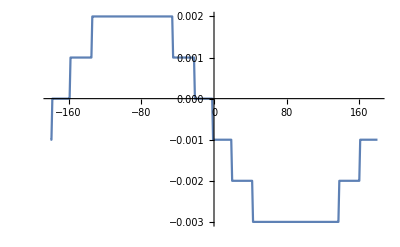

```mathematica
ListLinePlot[adata]
```

### Potentials

```mathematica
(*Data batch generated at:2020-08-03 10:06:10.083934*)potential1={{-8.0,7.794},{-7.75,-0.582},{-7.5,-9.642},{-7.25,-18.181},{-7.0,-24.665},{-6.75,-27.68},{-6.5,-26.495},{-6.25,-21.402},{-6.0,-13.578},{-5.75,-4.574},{-5.5,4.222},{-5.25,11.879},{-5.0,17.949},{-4.75,22.351},{-4.5,25.233},{-4.25,26.869},{-4.0,27.603},{-3.75,27.803},{-3.5,27.796},{-3.25,27.79},{-3.0,27.809},{-2.75,27.681},{-2.5,27.096},{-2.25,25.691},{-2.0,23.113},{-1.75,19.066},{-1.5,13.369},{-1.25,6.04},{-1.0,-2.566},{-0.75,-11.63},{-0.5,-19.851},{-0.25,-25.673},{0.0,-27.786},{0.25,-25.673},{0.5,-19.851},{0.75,-11.63},{1.0,-2.566},{1.25,6.04},{1.5,13.369},{1.75,19.066},{2.0,23.113},{2.25,25.691},{2.5,27.096},{2.75,27.681},{3.0,27.809},{3.25,27.79},{3.5,27.796},{3.75,27.803},{4.0,27.603},{4.25,26.869},{4.5,25.233},{4.75,22.351},{5.0,17.949},{5.25,11.879},{5.5,4.222},{5.75,-4.574},{6.0,-13.578},{6.25,-21.402},{6.5,-26.495},{6.75,-27.68},{7.0,-24.665},{7.25,-18.181},{7.5,-9.642},{7.75,-0.582},{8.0,7.794}};
(*Data batch generated at:2020-08-03 10:06:10.084142*)
potential2={{-8.0,8.659},{-7.75,-7.133},{-7.5,-23.25},{-7.25,-36.891},{-7.0,-44.989},{-6.75,-45.424},{-6.5,-38.077},{-6.25,-24.889},{-6.0,-8.891},{-5.75,7.043},{-5.5,20.956},{-5.25,31.908},{-5.0,39.72},{-4.75,44.648},{-4.5,47.168},{-4.25,47.882},{-4.0,47.49},{-3.75,46.736},{-3.5,46.263},{-3.25,46.408},{-3.0,47.072},{-2.75,47.754},{-2.5,47.744},{-2.25,46.305},{-2.0,42.778},{-1.75,36.612},{-1.5,27.411},{-1.25,15.078},{-1.0,0.09},{-0.75,-16.179},{-0.5,-31.312},{-0.25,-42.233},{0.0,-46.237},{0.25,-42.233},{0.5,-31.312},{0.75,-16.179},{1.0,0.09},{1.25,15.078},{1.5,27.411},{1.75,36.612},{2.0,42.778},{2.25,46.305},{2.5,47.744},{2.75,47.754},{3.0,47.072},{3.25,46.408},{3.5,46.263},{3.75,46.736},{4.0,47.49},{4.25,47.882},{4.5,47.168},{4.75,44.648},{5.0,39.72},{5.25,31.908},{5.5,20.956},{5.75,7.043},{6.0,-8.891},{6.25,-24.889},{6.5,-38.077},{6.75,-45.424},{7.0,-44.989},{7.25,-36.891},{7.5,-23.25},{7.75,-7.133},{8.0,8.659}};
(*Data batch generated at:2020-08-03 10:06:10.084342*)
potential3={{-8.0,-0.813},{-7.75,-27.544},{-7.5,-51.536},{-7.25,-67.215},{-7.0,-70.193},{-6.75,-59.571},{-6.5,-38.459},{-6.25,-12.247},{-6.0,13.89},{-5.75,36.509},{-5.5,54.076},{-5.25,66.393},{-5.0,73.944},{-4.75,77.482},{-4.5,77.88},{-4.25,76.168},{-4.0,73.583},{-3.75,71.445},{-3.5,70.791},{-3.25,71.94},{-3.0,74.334},{-2.75,76.805},{-2.5,78.03},{-2.25,76.831},{-2.0,72.229},{-1.75,63.383},{-1.5,49.594},{-1.25,30.516},{-1.0,6.658},{-0.75,-19.942},{-0.5,-45.274},{-0.25,-63.883},{0.0,-70.772},{0.25,-63.883},{0.5,-45.274},{0.75,-19.942},{1.0,6.658},{1.25,30.516},{1.5,49.594},{1.75,63.383},{2.0,72.229},{2.25,76.831},{2.5,78.03},{2.75,76.805},{3.0,74.334},{3.25,71.94},{3.5,70.791},{3.75,71.445},{4.0,73.583},{4.25,76.168},{4.5,77.88},{4.75,77.482},{5.0,73.944},{5.25,66.393},{5.5,54.076},{5.75,36.509},{6.0,13.89},{6.25,-12.247},{6.5,-38.459},{6.75,-59.571},{7.0,-70.193},{7.25,-67.215},{7.5,-51.536},{7.75,-27.544},{8.0,-0.813}};
(*Data batch generated at:2020-08-03 10:06:10.084547*)
potential4={{-8.0,-37.741},{-7.75,-74.744},{-7.5,-98.135},{-7.25,-100.751},{-7.0,-81.731},{-6.75,-47.061},{-6.5,-5.995},{-6.25,33.35},{-6.0,66.187},{-5.75,90.858},{-5.5,107.598},{-5.25,117.409},{-5.0,121.438},{-4.75,120.808},{-4.5,116.777},{-4.25,110.997},{-4.0,105.572},{-3.75,102.612},{-3.5,103.348},{-3.25,107.469},{-3.0,113.295},{-2.75,118.632},{-2.5,121.526},{-2.25,120.505},{-2.0,114.39},{-1.75,102.055},{-1.5,82.368},{-1.25,54.517},{-1.0,18.84},{-0.75,-21.929},{-0.5,-61.641},{-0.25,-91.33},{0.0,-102.426},{0.25,-91.33},{0.5,-61.641},{0.75,-21.929},{1.0,18.84},{1.25,54.517},{1.5,82.368},{1.75,102.055},{2.0,114.39},{2.25,120.505},{2.5,121.526},{2.75,118.632},{3.0,113.295},{3.25,107.469},{3.5,103.348},{3.75,102.612},{4.0,105.572},{4.25,110.997},{4.5,116.777},{4.75,120.808},{5.0,121.438},{5.25,117.409},{5.5,107.598},{5.75,90.858},{6.0,66.187},{6.25,33.35},{6.5,-5.995},{6.75,-47.061},{7.0,-81.731},{7.25,-100.751},{7.5,-98.135},{7.75,-74.744},{8.0,-37.741}};
```

## Computing the triaxial potential and its chiral partner

### Compare the values with the python implementation

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
IF[moi_]:=1/(2*moi);
j1[j_,theta_]:=j *Cos[theta*π/180];
j2[j_,theta_]:=j *Sin[theta*π/180];
AFct[I_,I1_,I2_,j_,theta_]:=IF[I2](1-j2[j,theta]/I)-IF[I1];
uFct[I_,I1_,I2_,I3_,j_,theta_]:=(IF[I3]-IF[I1])/AFct[I,I1,I2,j,theta];
v0Fct[I_,I1_,I2_,j_,theta_]:=(-IF[I1]*j1[j,theta])/AFct[I,I1,I2,j,theta];
kFct[I_,I1_,I2_,I3_,j_,theta_]:=Sqrt[uFct[I,I1,I2,I3,j,theta]];
```

### Computing the Jacobi Amplitude φ(q,k)

```mathematica
JA[q_,k_]:=If[Im[JacobiAmplitude[q,k^2]]≤10^(-11),Re[JacobiAmplitude[q,k^2]],NaN];
s[q_,k_]:=Sin[If[JA[q,k]==NaN,NaN,Re[JA[q,k]]]];
c[q_,k_]:=Cos[If[JA[q,k]==NaN,NaN,Re[JA[q,k]]]];
d[q_,k_]:=Sqrt[If[s[q,k]==NaN,NaN,Re[1-k^2*s[q,k]^2]]];
VRotor[q_,I_,I1_,I2_,I3_,j_,theta_]:=If[Im[(I(I+1)*kFct[I,I1,I2,I3,j,theta]^2+v0Fct[I,I1,I2,j,theta]^2)s[q,kFct[I,I1,I2,I3,j,theta]]^2+(2I+1)*v0Fct[I,I1,I2,j,theta]*c[q,kFct[I,I1,I2,I3,j,theta]]*d[q,kFct[I,I1,I2,I3,j,theta]]]≤10^(-11),Re[(I(I+1)*kFct[I,I1,I2,I3,j,theta]^2+v0Fct[I,I1,I2,j,theta]^2)s[q,kFct[I,I1,I2,I3,j,theta]]^2+(2I+1)*v0Fct[I,I1,I2,j,theta]*c[q,kFct[I,I1,I2,I3,j,theta]]*d[q,kFct[I,I1,I2,I3,j,theta]]],NaN];
```

```mathematica
params={9.5,80,100,90,5.5,-80};
(*VRotor[1,params[[1]],params[[2]],params[[3]],params[[4]],params[[5]],params[[6]]]*)
Manipulate[ListLinePlot[{Table[{q,VRotor[q,spin,params[[2]],params[[3]],params[[4]],params[[5]],params[[6]]]},{q,-8,8,0.1}]},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameLabel->{"q","V(q)"},Epilog->Inset[Style[StringTemplate["I=`` ℏ"][spin],18,Bold,Black],Scaled[{0.3,0.4}]]],{spin,5.5,22.5,2}]
```

General::munfl: ArcSin[0.866734-3.48861×10^-18 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcSin[0.57263+6.54693×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.